## Risk Assessment using Coupled Mean

### Introduction

The weighted generalized mean has been used to evaluate probabilistic forecasted.  The power of the mean is the degree of relative risk tolerance. The result Risk Profile has provided useful insights into the performance of machine learning and other probabilistic algorithms. Two issues need to be addressed with this approach to risk-biased assessment:
	1) The risk profile is only ‘proper’ for r = 0.  While the local nature of the assessment has been the priority, this does mean that optimization of an algorithm for r ≠ 0 will be biased. This may not be a problem since the point is to account for relative risk; however, a better understand of the difference between the risk profile and related proper scores would be valuable.
	2) A more serious concern is that the risk profile does not fulfil the generalized triangular relationship between cross-entropy (CE), entropy (E) and divergence (D). In the probability domain for r = 0, P_CE=P_E P_D. A related function should hold for r ≠ 0, P_CE^r=P_E^r⊗_r P_D^r. Unfortunately, the generalized mean using weights of 1/Nresults in the possibility that P_CE^r>P_E^r which violates the necessity of 0 ⩽ P_D^r⩽ 1.
	To address this issue this notebook will explore a definition of the ‘Coupled Mean’ which follows the theoretical development of the coupled algebra more closely. The derivation of the generalized mean from the generalized cross-entropy relied on the fact that probability of a test sample is 1/N. Because all the samples have the same probability the role of the escort or coupled Probability cancelled out. If instead the probability of a sample is treated as a function of the outcome probability from the histogram analysis, then the coupled Probability would be an important factor.  
	
	For a set {1,2,...,i,...,N} of test samples with {1,2,...,j,...,M} classes arranged into {1,2,...,k,...,N_bins} bins, the outcome probability for the j^thclass of the k^th bin is p_jk=n_jk/N_k, where n_jk is the number of j outcomes and N_k=∑_(j=1)^M n_jk is the total outcomes for the  k^thbin. The weights for computing the coupled mean (also a probability) are determined by normalizing the outcome probabilities over all the samples, w_jk=n_jk/N_k N_k/N=n_jk/N.
	From (Nelson, 2017) the following relationship is defined for the coupled average uncertainty for forecasts q, here in terms of r = -ακ/(1+κ) and referred to as the coupled mean

#### Frequency and Probability Computation per Bin

For a set {1,2,...,i,...,N} of test events with {1,2,...,j,...,M} classes per event, the probabilities are sorted and arranged into {1,2,...,k,...,K} bins. It is also possible, though not necessary for the algorithm to described in terms of separate bins for each class. For each true event class j*, i.e. the event that actually happened, the outcome probability for the j^(*th) class of the k^th bin is p_(j^*k)=(n_(j^*k))/N_k N_k/N=(n_(j^*k))/N, where n_(j^*k) is the number of probabilities in the k^th bin for the true event j^* and N_k=∑_(j=1)^M n_jk is the total outcomes for the  k^thbin. The outcome probability is also the weight for the coupled mean computations, w_(j^*k)=p_(j^*k)The average forecasted probability (or quoted (q) probability) for each bin and class is computed using the geometric of the forecasts for the true events, q_(j^*k)=∏_(i=1)^N (q_(ij^*k))^(p_(j^*k)).  (Can this notation be improved?  It’s an increment through the ij^* probability samples in the k^th bin rather than all the test events).  Use of the weight p_(j^*k) rather than assuming independence of each event with 1/Nchanges the composition of the metrics.

#### Equiprobability, Accuracy, Robustness and Decisiveness Metrics

From (Nelson, 2017) the following relationship is defined for the coupled average uncertainty for forecasts q and outcome frequencies p, in terms of the relative risk aversion r = ακ/(1+κ) and referred to as the coupled mean

(Q̄)_r=((∑_(k=1)^K ∑_(j^*=1)^M w_(j^*k)^(1+r)q_(j^*k)^-r)/(∑_(k=1)^K ∑_(j^*=1)^M w_(j^*k)^(1+r)))^(-1/r) and (P̄)_r=((∑_(k=1)^K ∑_(j^*=1)^M w_(j^*k)^(1+r)p_(j^*k)^-r)/(∑_(k=1)^K ∑_(j^*=1)^M w_(j^*k)^(1+r)))^(-1/r).

The original Risk Assessment was derived from a computation of the Coupled Average Uncertainty of a distribution and then substitute 1/Nfor the weight. This derivation is shown in equations (32-33) of (Nelson, 2017). Advancing the metric by accounting for the frequency of outcomes, requires w_(j^*k)=p_(j^*k),

(Q̄)_r=((∑_(k=1)^K ∑_(j^*=1)^M p_(j^*k)^(1+r)q_(j^*k)^-r)/(∑_(k=1)^K ∑_(j^*=1)^M p_(j^*k)^(1+r)))^(-1/r) and (P̄)_r=((∑_(k=1)^K ∑_(j^*=1)^M p_(j^*k))/(∑_(k=1)^K ∑_(j^*=1)^M p_(j^*k)^(1+r)))^(-1/r)

Note:  This derivation is different than what is implemented below.  For this reason, the results below are going to be reproduced using this more precise derivation.  The difference arises from the fact that the implementation below started with equation 33 of (Nelson, 2017) and then substituted p_(j^*k) for the weights; however, the more careful derivation started with the cross-entropy rather than the entropy function.

### References

(Nelson, et. al. 2017) K. P. Nelson, S. R. Umarov, and M. A. Kon, “On the average uncertainty for systems with nonlinear coupling,” Phys. A Stat. Mech. its Appl., vol. 468, pp. 30–43, 2017.

## Example Using Precipitation Forecasts

The Import Media Forecast Data Section copied from NOAA Forecasting v6

Follows the functions from Election Assessment with some modification of the names
	prevBin -> outcomeProb; geoBin -> forecastProbs
	prevAll -> geoMeanOutcome; geoAll -> geoMeanForecast; divAll -> divergenceProb

The functions are self-contained within this file

### Import Media Forecast Data

The dataset includes 321 forecasts for rain or no rain, one to seven days in advance.  Each rain forecast is for a particular percentile {0,5,10,15,20,30,40,50,60,70,80,90,100}.  To facilitate analysis the 0% and 100% need to be adjusted. By observation, the actual forecasts were on the order of 0.1% and 99.9% so these will be used initially.  Also, the 5% and 15% rain forecasts require the corresponding 95% and 85% no rain percentiles, so these are added as categories.

Data is imported as a 39 by 14 array.  Row spaces added to keep data in 10 row segments
	Rows 2-9: Station 1 Forecasts
	Rows 12-19: Station 1 Rain Days
	Rows 22-29: Station 2 Forecasts
	Rows 32-39: Station 2 Rain Days

```mathematica
Folder = "/Users/kenricnelson/Documents/Photrek/Business Development/Pursuits/NOAA Tornado Forecasting/";
MediaForecastData=Import[Folder<>"Precipitation Forecasts.xlsx"]⟦1⟧/.x_Real->Floor[x];
```

```mathematica
Forecasts = {Riffle[MediaForecastData⟦#,2;;14⟧,0,{-4,-2,2}]&/@Table[i,{i,3,9}],
Riffle[MediaForecastData⟦#,2;;14⟧,0,{-4,-2,2}]&/@Table[i,{i,23,29}]}/.x_/;x==0->"NA";
DaysAhead=MediaForecastData⟦3;;9,1⟧;
Percentiles = Riffle[ReplacePart[MediaForecastData⟦2,2;;14⟧//Floor,
{1->1,13->99}],{85,95},{12,14,2}];
(* Append Baseline as third list *)
AppendTo[Forecasts,Table["NA",5,15]];
Forecasts⟦3,1,4⟧=Forecasts⟦3,2,5⟧=Total[MediaForecastData⟦3,2;;14⟧];
Forecasts⟦3,{3,4,5},1;;7⟧=Reverse[Forecasts⟦1,{1,4,7},1;;7⟧,2];
Forecasts⟦3,{3,4,5},8⟧=Forecasts⟦1,{1,4,7},8⟧;
Forecasts⟦3,{3,4,5},9;;15⟧=Reverse[Forecasts⟦1,{1,4,7},9;;15⟧,2];
BaselineLabel = {"B1","B2", "U1", "U4", "U7"};

Print["Forecasts per Percentile for Station 1"];
TableForm[Forecasts⟦1⟧,
TableHeadings->{DaysAhead,Percentiles}
]
Print["Forecasts per Percentile for Station 2"]
TableForm[Forecasts⟦2⟧,
TableHeadings->{DaysAhead,Percentiles}
]
Print["Forecasts per Percentile for Baseline"]
TableForm[Forecasts⟦3⟧,
TableHeadings->{BaselineLabel,Percentiles}
]
```

Forecasts per Percentile for Station 1

| 1 | 5 | 10 | 15 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 85 | 90 | 95 | 99
D1 | 162 | 1 | 10 | 15 | 37 | 36 | 16 | 12 | 18 | 4 | 4 | NA | 2 | NA | 4
D2 | 169 | NA | 4 | 20 | 32 | 42 | 25 | 10 | 14 | 4 | 1 | NA | NA | NA | NA
D3 | 176 | NA | 1 | 13 | 53 | 32 | 21 | 16 | 6 | 2 | NA | NA | NA | NA | 1
D4 | 172 | NA | 1 | 16 | 51 | 37 | 29 | 13 | 2 | NA | NA | NA | NA | NA | NA
D5 | 169 | NA | 2 | 10 | 78 | 39 | 15 | 7 | 1 | NA | NA | NA | NA | NA | NA
D6 | 181 | NA | NA | 13 | 71 | 43 | 9 | 3 | 1 | NA | NA | NA | NA | NA | NA
D7 | 140 | NA | NA | 16 | 117 | 40 | 8 | NA | NA | NA | NA | NA | NA | NA | NA

Forecasts per Percentile for Station 2

| 1 | 5 | 10 | 15 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 85 | 90 | 95 | 99
D1 | 170 | NA | 9 | NA | 58 | 28 | 24 | 9 | 10 | 6 | 5 | NA | 1 | NA | 1
D2 | 182 | NA | 8 | NA | 67 | 28 | 26 | 5 | 5 | NA | NA | NA | NA | NA | NA
D3 | 207 | NA | 7 | NA | 60 | 29 | 15 | 1 | 2 | NA | NA | NA | NA | NA | NA
D4 | 193 | NA | 8 | NA | 88 | 21 | 10 | 1 | NA | NA | NA | NA | NA | NA | NA
D5 | 202 | NA | 5 | NA | 82 | 24 | 8 | NA | NA | NA | NA | NA | NA | NA | NA
D6 | 212 | NA | 3 | NA | 92 | 12 | 2 | NA | NA | NA | NA | NA | NA | NA | NA
D7 | 233 | NA | 1 | NA | 80 | 7 | NA | NA | NA | NA | NA | NA | NA | NA | NA

Forecasts per Percentile for Baseline

| 1 | 5 | 10 | 15 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 85 | 90 | 95 | 99
B1 | NA | NA | NA | 321 | NA | NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
B2 | NA | NA | NA | NA | 321 | NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
U1 | 16 | 36 | 37 | 15 | 10 | 1 | 162 | 12 | 4 | NA | 2 | NA | 4 | 4 | 18
U4 | 29 | 37 | 51 | 16 | 1 | NA | 172 | 13 | NA | NA | NA | NA | NA | NA | 2
U7 | 8 | 40 | 117 | 16 | NA | NA | 140 | NA | NA | NA | NA | NA | NA | NA | NA

```mathematica
ForecastRain ={ 
Riffle[Quiet[MediaForecastData⟦#,2;;14⟧/
MediaForecastData⟦#-10,2;;14⟧],
"NA",{-4,-2,2}]&/@Table[i,{i,13,19}]/.{Indeterminate->"NA",0->0.01,1->0.99},
Riffle[Quiet[MediaForecastData⟦#,2;;14⟧/
MediaForecastData⟦#-10,2;;14⟧],
"NA",{-4,-2,2}]&/@Table[i,{i,33,39}]/.{Indeterminate->"NA",0->0.01,1->0.99},
Table["NA",5,15]
};
ForecastRain⟦3,1,4⟧=ForecastRain⟦3,2,5⟧=Total[MediaForecastData⟦13,2;;14⟧]/Forecasts⟦3,1,4⟧;
ForecastRain⟦3,{3,4,5},1;;7⟧=Reverse[ForecastRain⟦1,{1,4,7},1;;7⟧,2];
ForecastRain⟦3,{3,4,5},8⟧=ForecastRain⟦1,{1,4,7},8⟧;
ForecastRain⟦3,{3,4,5},9;;15⟧=Reverse[ForecastRain⟦1,{1,4,7},9;;15⟧,2];

Print["Fraction of Rain Days for Station 1"];
TableForm[ForecastRain⟦1⟧,
TableHeadings->{DaysAhead,Percentiles}]
Print["Fraction of Rain Days for Station 2"];
TableForm[ForecastRain⟦2⟧,
TableHeadings->{DaysAhead,Percentiles}
]
Print["Fraction of Rain Days for Baseline"];
TableForm[ForecastRain⟦3⟧,
TableHeadings->{BaselineLabel,Percentiles}
]
```

Fraction of Rain Days for Station 1

| 1 | 5 | 10 | 15 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 85 | 90 | 95 | 99
D1 | 5/162 | 0.01 | 0.01 | 2/15 | 7/37 | 13/36 | 1/2 | 3/4 | 11/18 | 0.99 | 0.99 | NA | 1/2 | NA | 3/4
D2 | 10/169 | NA | 1/4 | 3/10 | 5/32 | 2/7 | 12/25 | 3/5 | 11/14 | 3/4 | 0.99 | NA | NA | NA | NA
D3 | 5/44 | NA | 0.01 | 0.01 | 11/53 | 13/32 | 11/21 | 3/8 | 5/6 | 0.01 | NA | NA | NA | NA | 0.99
D4 | 5/43 | NA | 0.01 | 1/8 | 14/51 | 11/37 | 16/29 | 3/13 | 1/2 | NA | NA | NA | NA | NA | NA
D5 | 19/169 | NA | 0.01 | 1/5 | 10/39 | 16/39 | 7/15 | 2/7 | 0.99 | NA | NA | NA | NA | NA | NA
D6 | 24/181 | NA | NA | 2/13 | 21/71 | 14/43 | 4/9 | 1/3 | 0.99 | NA | NA | NA | NA | NA | NA
D7 | 1/5 | NA | NA | 1/8 | 22/117 | 13/40 | 1/4 | NA | NA | NA | NA | NA | NA | NA | NA

Fraction of Rain Days for Station 2

| 1 | 5 | 10 | 15 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 85 | 90 | 95 | 99
D1 | 7/170 | NA | 0.01 | NA | 6/29 | 3/7 | 3/8 | 7/9 | 9/10 | 5/6 | 4/5 | NA | 0.99 | NA | 0.99
D2 | 8/91 | NA | 0.01 | NA | 19/67 | 9/28 | 15/26 | 4/5 | 4/5 | NA | NA | NA | NA | NA | NA
D3 | 25/207 | NA | 3/7 | NA | 7/30 | 18/29 | 1/3 | 0.01 | 0.99 | NA | NA | NA | NA | NA | NA
D4 | 22/193 | NA | 3/8 | NA | 7/22 | 1/3 | 7/10 | 0.01 | NA | NA | NA | NA | NA | NA | NA
D5 | 29/202 | NA | 0.01 | NA | 27/82 | 1/3 | 3/8 | NA | NA | NA | NA | NA | NA | NA | NA
D6 | 19/106 | NA | 1/3 | NA | 21/92 | 1/2 | 1/2 | NA | NA | NA | NA | NA | NA | NA | NA
D7 | 47/233 | NA | 0.01 | NA | 19/80 | 1/7 | NA | NA | NA | NA | NA | NA | NA | NA | NA

Fraction of Rain Days for Baseline

| 1 | 5 | 10 | 15 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 85 | 90 | 95 | 99
B1 | NA | NA | NA | 67/321 | NA | NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
B2 | NA | NA | NA | NA | 67/321 | NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
U1 | 1/2 | 13/36 | 7/37 | 2/15 | 0.01 | 0.01 | 5/162 | 3/4 | 3/4 | NA | 1/2 | NA | 0.99 | 0.99 | 11/18
U4 | 16/29 | 11/37 | 14/51 | 1/8 | 0.01 | NA | 5/43 | 3/13 | NA | NA | NA | NA | NA | NA | 1/2
U7 | 1/4 | 13/40 | 22/117 | 1/8 | NA | NA | 1/5 | NA | NA | NA | NA | NA | NA | NA | NA

```mathematica
ForecastNonRain = {
Reverse[ForecastRain⟦1⟧/.x_/;NumericQ[x]->1-x,2],
Reverse[ForecastRain⟦2⟧/.x_/;NumericQ[x]->1-x,2],
Table["NA",5,15]
};
ForecastNonRain⟦3,1,-4⟧=ForecastNonRain⟦3,2,-5⟧=1-ForecastRain⟦3,1,4⟧;
ForecastNonRain⟦3,{3,4,5},1;;7⟧=Reverse[ForecastNonRain⟦1,{1,4,7},1;;7⟧,2];
ForecastNonRain⟦3,{3,4,5},8⟧=ForecastNonRain⟦1,{1,4,7},8⟧;
ForecastNonRain⟦3,{3,4,5},9;;15⟧=Reverse[ForecastNonRain⟦1,{1,4,7},9;;15⟧,2];

Print["Fraction of non-Rain Days for Station 1"]
TableForm[ForecastNonRain⟦1⟧,
TableHeadings->{DaysAhead,Percentiles}
]
Print["Fraction of non-Rain Days for Station 2"]
TableForm[ForecastNonRain⟦2⟧,
TableHeadings->{DaysAhead,Percentiles}
]
Print["Fraction of non-Rain Days for Baseline"]
TableForm[ForecastNonRain⟦3⟧,
TableHeadings->{BaselineLabel,Percentiles}
]
```

Fraction of non-Rain Days for Station 1

| 1 | 5 | 10 | 15 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 85 | 90 | 95 | 99
D1 | 1/4 | NA | 1/2 | NA | 0.01 | 0.01 | 7/18 | 1/4 | 1/2 | 23/36 | 30/37 | 13/15 | 0.99 | 0.99 | 157/162
D2 | NA | NA | NA | NA | 0.01 | 1/4 | 3/14 | 2/5 | 13/25 | 5/7 | 27/32 | 7/10 | 3/4 | NA | 159/169
D3 | 0.01 | NA | NA | NA | NA | 0.99 | 1/6 | 5/8 | 10/21 | 19/32 | 42/53 | 0.99 | 0.99 | NA | 39/44
D4 | NA | NA | NA | NA | NA | NA | 1/2 | 10/13 | 13/29 | 26/37 | 37/51 | 7/8 | 0.99 | NA | 38/43
D5 | NA | NA | NA | NA | NA | NA | 0.01 | 5/7 | 8/15 | 23/39 | 29/39 | 4/5 | 0.99 | NA | 150/169
D6 | NA | NA | NA | NA | NA | NA | 0.01 | 2/3 | 5/9 | 29/43 | 50/71 | 11/13 | NA | NA | 157/181
D7 | NA | NA | NA | NA | NA | NA | NA | NA | 3/4 | 27/40 | 95/117 | 7/8 | NA | NA | 4/5

Fraction of non-Rain Days for Station 2

| 1 | 5 | 10 | 15 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 85 | 90 | 95 | 99
D1 | 0.01 | NA | 0.01 | NA | 1/5 | 1/6 | 1/10 | 2/9 | 5/8 | 4/7 | 23/29 | NA | 0.99 | NA | 163/170
D2 | NA | NA | NA | NA | NA | NA | 1/5 | 1/5 | 11/26 | 19/28 | 48/67 | NA | 0.99 | NA | 83/91
D3 | NA | NA | NA | NA | NA | NA | 0.01 | 0.99 | 2/3 | 11/29 | 23/30 | NA | 4/7 | NA | 182/207
D4 | NA | NA | NA | NA | NA | NA | NA | 0.99 | 3/10 | 2/3 | 15/22 | NA | 5/8 | NA | 171/193
D5 | NA | NA | NA | NA | NA | NA | NA | NA | 5/8 | 2/3 | 55/82 | NA | 0.99 | NA | 173/202
D6 | NA | NA | NA | NA | NA | NA | NA | NA | 1/2 | 1/2 | 71/92 | NA | 2/3 | NA | 87/106
D7 | NA | NA | NA | NA | NA | NA | NA | NA | NA | 6/7 | 61/80 | NA | 0.99 | NA | 186/233

Fraction of non-Rain Days for Baseline

| 1 | 5 | 10 | 15 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 85 | 90 | 95 | 99
B1 | NA | NA | NA | NA | NA | NA | NA | NA | NA | NA | NA | 254/321 | NA | NA | NA
B2 | NA | NA | NA | NA | NA | NA | NA | NA | NA | NA | 254/321 | NA | NA | NA | NA
U1 | 7/18 | 0.01 | 0.01 | NA | 1/2 | NA | 1/4 | 1/4 | 157/162 | 0.99 | 0.99 | 13/15 | 30/37 | 23/36 | 1/2
U4 | 1/2 | NA | NA | NA | NA | NA | NA | 10/13 | 38/43 | NA | 0.99 | 7/8 | 37/51 | 26/37 | 13/29
U7 | NA | NA | NA | NA | NA | NA | NA | NA | 4/5 | NA | NA | 7/8 | 95/117 | 27/40 | 3/4

### Rain Forecast Risk Assessment with Coupled Mean

```mathematica
numMeans = 7;  (* Assumed odd, so that zero included *)
Lim=1;
positiveRiskValues =Range[0,Lim,2*Lim/(numMeans-1)];
negativeRiskValues = (-2Drop[positiveRiskValues,1])/(2+Drop[positiveRiskValues,1]);
(* riskValues are the relative risk aversion *)
riskValues = -Reverse[negativeRiskValues]~Join~positiveRiskValues
```

{2/3,1/2,2/7,0,-1/3,-2/3,-1}

Compute a Table of Overall Statistics with dimension {numMeans, 3} where the three values are: outcomeProb, forecastProb, divergenceProb

```mathematica
TVStation = 3;ForecastRows=5;
TotalForecasts = Total[Forecasts,{3}]/.x_/;x=="NA"->0;
weatherForecastMetrics=ComputeCoupledMeanNOAA[
Transpose[{ForecastRain⟦TVStation⟧,ForecastNonRain⟦TVStation⟧},{3,2,1}],
Transpose[Table[Percentiles/100,ForecastRows,2],{2,3,1}],
Transpose[{ForecastRain⟦TVStation⟧Forecasts⟦TVStation⟧/TotalForecasts[[TVStation]],ForecastNonRain⟦TVStation⟧Reverse[Forecasts⟦TVStation⟧,2]/TotalForecasts[[TVStation]]},
{3,2,1}],
#
]&/@riskValues;
(*
weatherForecastMetricsBasedonCoupledEntropy=ComputeCoupledMeanNOAA[
Transpose[{ForecastRain⟦TVStation⟧,ForecastNonRain⟦TVStation⟧},{3,2,1}],
Transpose[Table[Percentiles/100,ForecastRows,2],{2,3,1}],
Transpose[{ForecastRain⟦TVStation⟧Forecasts⟦TVStation⟧/TotalForecasts[[TVStation]],ForecastNonRain⟦TVStation⟧Reverse[Forecasts⟦TVStation⟧,2]/TotalForecasts[[TVStation]]},
{3,2,1}],
#
]&/@riskValues;
*)
```

Extract the Robust (-2/3), Accuracy (0), and Decisive (1) metrics from the weatherForecastMetrics

```mathematica
RobustMetrics = weatherForecastMetrics⟦1⟧;
AccuracyMetrics=weatherForecastMetrics⟦Ceiling[numMeans/2]⟧;
DecisiveMetrics = weatherForecastMetrics⟦-1⟧;
```

#### Risk Assessment using Coupled Mean of Rain Forecasts

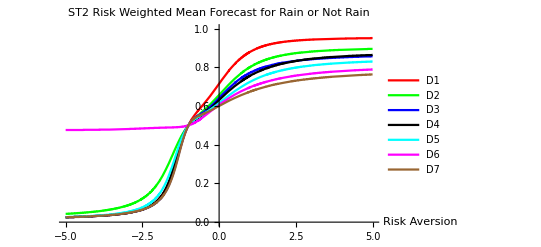

```mathematica
TVStation=2; numberDays=7;
ForecastStats=2; OutcomeStats=1;
rMin=-5;rMax=5;
TotalForecasts = Total[Forecasts,{3}]/.x_/;x=="NA"->0;
Colors={Red, Green, Blue, Black, Cyan, Magenta, Brown};
Show@@Table[
Plot[Legended[ComputeCoupledMeanNOAA[
Transpose[{ForecastRain⟦TVStation⟧,ForecastNonRain⟦TVStation⟧},{3,2,1}],
Transpose[Table[Percentiles/100,numberDays,2],{2,3,1}],
Transpose[{ForecastRain⟦TVStation⟧Forecasts⟦TVStation⟧/TotalForecasts⟦TVStation⟧,ForecastNonRain⟦TVStation⟧Reverse[Forecasts⟦TVStation⟧,2]/TotalForecasts⟦TVStation⟧},
{3,2,1}],
Risk
]⟦OutcomeStats,DayAhead⟧,DaysAhead⟦DayAhead⟧],
{Risk,rMin,rMax},
PlotRange->{{rMin,rMax},{0,1}},
PlotStyle->Colors⟦DayAhead⟧,
AxesStyle->{Medium,Bold},
AxesLabel->{"Risk Aversion",None},
PlotLabel-> "ST"<>ToString[TVStation]<>" Risk Weighted Mean Forecast for Rain or Not Rain ",
TicksStyle->{Bold,Medium}
],
{DayAhead,numberDays}]
```

#### Rain Forecast Assessment Results

Results are shown for Risk Bias values between -5 and 5; however, published results will focus on -1 to 1.
	1 - Always equal to the inverse of the number of states
	0 - Geometric Mean associated with Shannon Entropy
	-2/3 - Metric used to define Robustness
	1 - Use of the Coupled Mean extends the range of useful negative values.

TV Station 1

Forecast Statistics

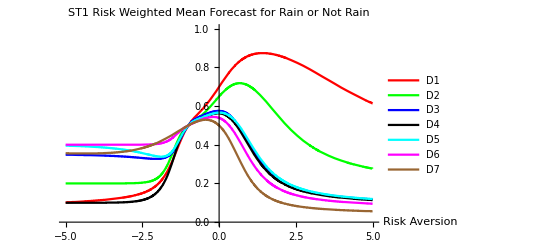

Outcome Statistics

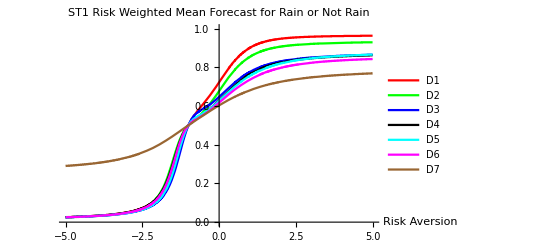

TV Station 2

Forecast Statistics

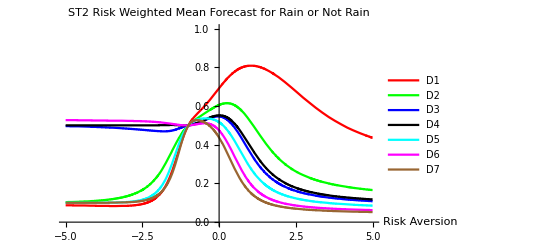

Outcome Statistics

-Graphics-

Baseline Forecasts
Forecast Statistics

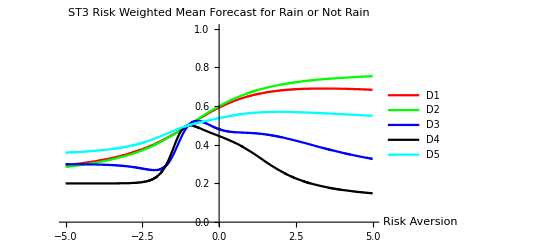

Outcome Statistics

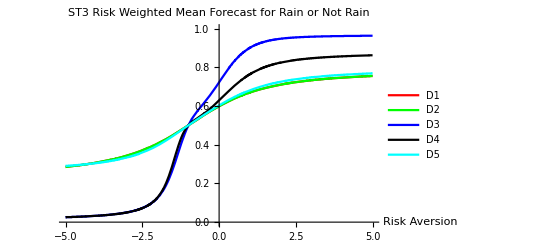

### Forecast vs. Source Assessment of Rain Forecasts

Follows the functions from Election Assessment with some modification of the names
	prevBin -> outcomeProb; geoBin -> forecastProbs
	prevAll -> geoMeanOutcome; geoAll -> geoMeanForecast; divAll -> divergenceProb
Calls functions from “Assess Probabilities v7”
Uses inputs from the “Import Media Forecast Data” Section
Does not use the “Compute Generalized Mean of Forecasts” Section which will be superseded by this section

Generate complementary values of risk for the generalized mean computation

```mathematica
numMeans = 11;  (* Assumed odd, so that zero included *)
Lim=1;
positiveRiskValues =Range[0,Lim,2*Lim/(numMeans-1)];
(*negativeRiskValues =-Drop[positiveRiskValues,1];*)
negativeRiskValues = (-2Drop[positiveRiskValues,1])/(2+Drop[positiveRiskValues,1]);
(* riskValues are the relative risk aversion *)
riskValues = -Reverse[negativeRiskValues]~Join~positiveRiskValues
```

{2/3,4/7,6/13,1/3,2/11,0,-1/5,-2/5,-3/5,-4/5,-1}

Compute a Table of Overall Statistics with dimension {numMeans, 3} where the three values are: outcomeProb, forecastProb, divergenceProb

```mathematica
TVStation = 3;ForecastRows=5;
TotalForecasts = Total[Forecasts,{3}]/.x_/;x=="NA"->0;
(* weatherForecastMetrics Dimensions: 7 days; 3 metrics; 5 riskValues *)
weatherForecastMetrics=ComputeCoupledMeanNOAA[
Transpose[{ForecastRain⟦TVStation⟧,ForecastNonRain⟦TVStation⟧},{3,2,1}],Transpose[Table[Percentiles/100,ForecastRows,2],{2,3,1}],
Transpose[{ForecastRain⟦TVStation⟧Forecasts⟦TVStation⟧/TotalForecasts[[TVStation]],ForecastNonRain⟦TVStation⟧Reverse[Forecasts⟦TVStation⟧,2]/TotalForecasts[[TVStation]]},
{3,2,1}],
#
]&/@riskValues;
```

Extract the Robust (-2/3), Accuracy (0), and Decisive (1) metrics from the weatherForecastMetrics

```mathematica
RobustMetrics = weatherForecastMetrics⟦1⟧;
AccuracyMetrics=weatherForecastMetrics⟦Ceiling[numMeans/2]⟧;
DecisiveMetrics = weatherForecastMetrics⟦-1⟧;
```

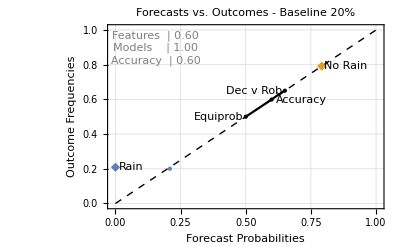

```mathematica
Show[
(* Plot the raw forecasts and outcomes for rain and not rain *)
DayOut=2;
ListPlot[{
Flatten[{ForecastRain⟦TVStation⟧⟦#⟧,Percentiles/100}&/@{DayOut},1]//Transpose,
Flatten[{ForecastNonRain⟦TVStation⟧⟦#⟧,Percentiles/100}&/@{DayOut},1]//Transpose
},
PlotRange->{{-0.01,1.01},{-0.01,1.01}},
(*PlotLegends->{"Rain","Not Rain"},*)
(*PlotLabel->Style["ST"<>ToString[TVStation]<>" Rain Outcomes vs. Forecasts - "<>ToString[DayOut]<>" Day"<>If[DayOut≠1,"s",""]<>" Out",
16, Black],*)
PlotLabel->Style[" Forecasts vs. Outcomes - Baseline"<>If[DayOut==1," 15%"," 20%"],
16, Black],
Frame->{{True, False},{True,False}},
FrameLabel->{"Forecast Probabilities","Outcome Frequencies"},
LabelStyle->Directive[12],
PlotStyle->PointSize[Medium],
GridLines->Automatic,
Epilog-> Inset[Style[
NumberForm[TableForm[
Flatten[Permute[
weatherForecastMetrics⟦Ceiling[Length[weatherForecastMetrics]/2],All,#⟧,
{1,3,2}]&/@{DayOut}],
TableHeadings->{{"Features ","Models   ","Accuracy "},None}],{2,2}],
Gray],
{0.154,0.895}]
], 
Graphics[{Dashed,Line[{{0,0},{1,1}}]}], (* Dashed line of equality *)
(* Plot the Robust, Accurate & Decisive Metrics *)
ListPlot[{
Labeled[{RobustMetrics⟦2,#⟧,RobustMetrics⟦1,#⟧},
"Dec v Rob ", Left],
Labeled[{AccuracyMetrics⟦2,#⟧,AccuracyMetrics⟦1,#⟧},
"  Accuracy", Right],
Labeled[{DecisiveMetrics⟦2,#⟧,DecisiveMetrics⟦1,#⟧},
"Equiprob ", Left]},
PlotRange->{{-0.01,1.01},{-0.01,1.01}},
PlotStyle->{PointSize[Large],Black}
]&/@{DayOut}, 
(* Plot the Generalized Means for Forecast and Outcome *)
ListPlot[weatherForecastMetrics⟦All,{2,1},#⟧,
Joined->True,InterpolationOrder->4,
PlotStyle->Black
]&/@{DayOut}, 

(* Plot the Classification for Rain or NonRain *)
numRainForecasts = Round[Total[(ForecastRain⟦TVStation⟧⟦#,All⟧*Forecasts⟦TVStation⟧⟦#,All⟧)]]&/@{DayOut};
numNonRainForecats = Round[Total[Reverse[Reverse[ForecastNonRain⟦TVStation⟧⟦#,All⟧]*Forecasts⟦TVStation⟧⟦#,All⟧]]]&/@{DayOut};
numForecasts=Total[Forecasts⟦TVStation⟧⟦#,All⟧]&/@{DayOut};

ListPlot[
{{
Labeled[{((0.5Total[Take[(ForecastRain⟦TVStation⟧⟦#,All⟧*Forecasts⟦TVStation⟧⟦#,All⟧),{8}]]+
Total[Take[(ForecastRain⟦TVStation⟧⟦#,All⟧*Forecasts⟦TVStation⟧⟦#,All⟧),-7]])/
numForecasts&/@{DayOut})⟦1,1⟧,(Total[ForecastRain⟦TVStation⟧⟦#,All⟧Forecasts⟦TVStation⟧⟦#,All⟧]/numForecasts&/@{DayOut})⟦1,1⟧
}/.x_/;x=="NA"->0, " Rain",{Right,Left}]
},
{
Labeled[{
((0.5Total[Take[Reverse[Reverse[ForecastNonRain⟦TVStation⟧⟦#,All⟧]*Forecasts⟦TVStation⟧⟦#,All⟧],{8}]]+
Total[Take[Reverse[Reverse[ForecastNonRain⟦TVStation⟧⟦#,All⟧]*Forecasts⟦TVStation⟧⟦#,All⟧],-7]])/
numForecasts&/@{DayOut})⟦1,1⟧,(Total[Reverse[Reverse[ForecastNonRain⟦TVStation⟧⟦#,All⟧]*Forecasts⟦TVStation⟧⟦#,All⟧]]/
numForecasts&/@{DayOut})⟦1,1⟧
}/.x_/;x=="NA"->0, " No Rain",{Right,Left}]
}
},
ngon[p_,q_]:=Polygon[Table[{Cos[2Pi k q/p],Sin[2Pi k q/p]},{k,p}]];
PlotMarkers->{{Graphics[ngon[4,1]],9},{Graphics[ngon[4,1]],9}}
]
]
```

#### Source vs. Forecast Assessment of Rain Forecast Results with negative Risk limit of -2/3

Station 1

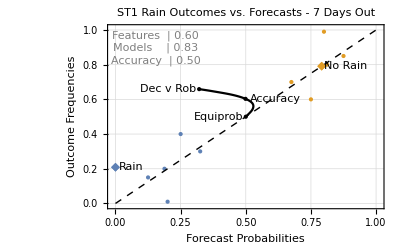

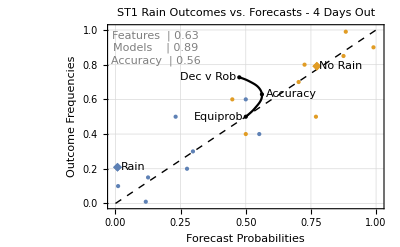

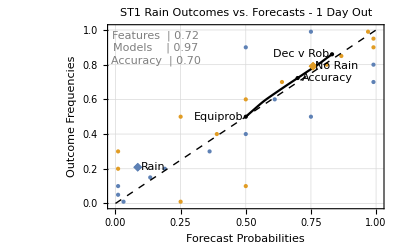

Station 2

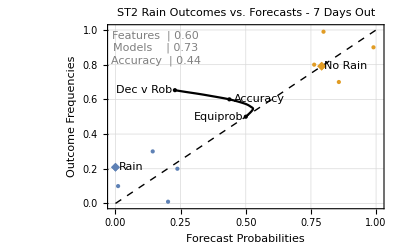

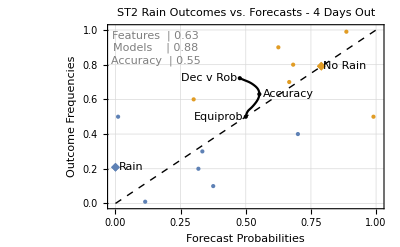

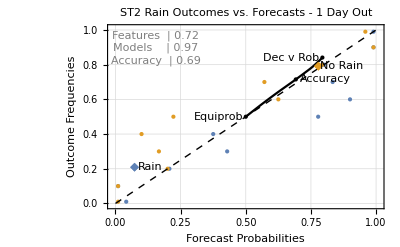

Baseline Forecasts

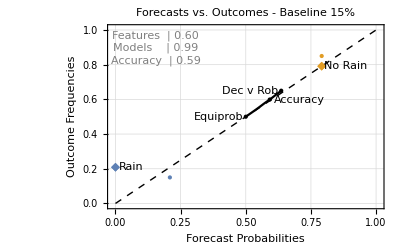

-Graphics-

#### Forecast vs. Source Assessment of Rain Forecasts Results Using Modification of Coupled Entropy rather than Coupled Cross Entropy

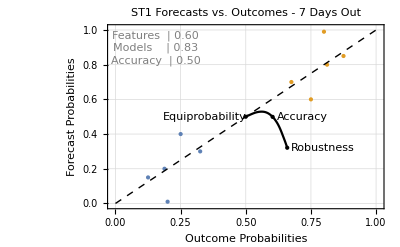

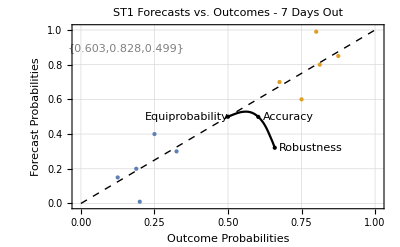

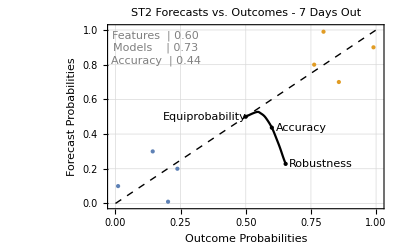

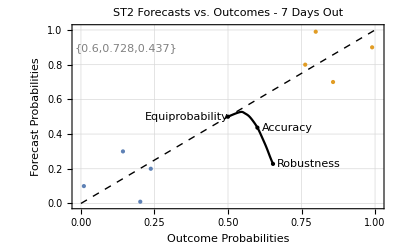

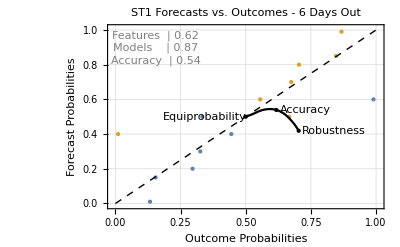

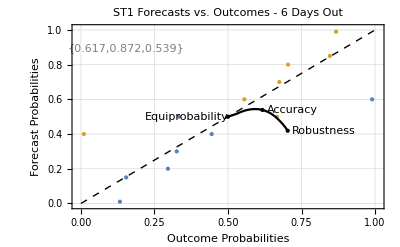

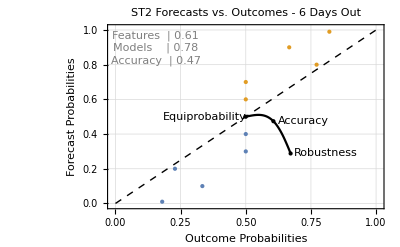

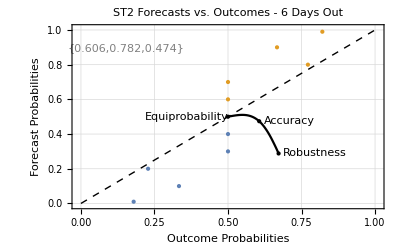

Baseline 20%

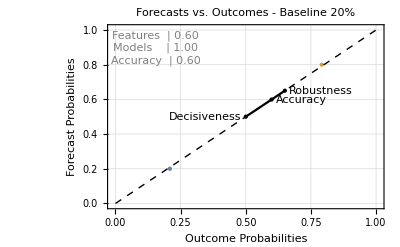

### Functions for Coupled Mean Computations

Approach will be to modify the ComputeOverallStats NOAA function

```mathematica
ComputeCoupledMeanNOAA[prevBin_,geoBin_,weightBin_,metricPower_]:=Module[{overallStats,prev,geo,weight,weightedPrev,
numBins,numForecasters,numHypotheses},
{numBins,numForecasters,numHypotheses}=Dimensions[prevBin];

{prev,geo,weight}=ArrayReshape[Transpose[#,{2,1,3}],{numForecasters,numBins*numHypotheses}]&/@
{prevBin,geoBin,weightBin};
overallStats = ConstantArray[0,{2,numForecasters}];

Assert[True]; (* Debug Break Point *)
overallStats={
MapThread[CoupledCrossProb[ (* Frequencies, Forecasts, risk aversion *)
MapThread[Pick[#2,NumericQ[#1]]&,{#1,#2}],MapThread[Pick[#,NumericQ[#]]&,{#1}],
metricPower
]&,{prev,weight}],
MapThread[CoupledCrossProb[ (* Frequencies, Forecasts, risk aversion *)
MapThread[Pick[#2,NumericQ[#1]]&,{#1,#2}],MapThread[Pick[#2,NumericQ[#1]]&,{#1,#3}],
metricPower
]&,{prev,weight,geo}]
};
Round[
AppendTo[overallStats,overallStats⟦2⟧/overallStats⟦1⟧],
0.001
]
];
```

```mathematica
(* The CoupledMean takes as inputs:
1) discrete variable - X,
	2) discrete probability weights - P,
		3) relative risk aversion - r,
and outputs the Coupled Mean
	CoupledMean[X,r,P]=(∑_(i=1)^N Subscript[p, i]^(1+r)/(∑_(j=1)^N Subscript[p, i]^(1+r))Subscript[x, i]^r)^(1/r).
This is the weighted generalized mean with weights Subscript[p, i]^(1+r)/(∑_(j=1)^N Subscript[p, i]^(1+r)).
The CoupledCrossProbs[P,Q,r] is the Coupled Mean applied to probabilites Q.
CoupledCrossProb[P,Q,r]=CoupledMean[Q^-1,r,P]^-1. This function is also equal to CoupledExponential[-CoupledCrossEntropy[P,Q,κ,d,α],κ,d,α]

The CoupledDivergenceProbs[P,Q,r]=CoupledMean[P*Q^-1,r,P]^-1
The CoupledEntropyProbs[P,r]= CoupledMean[P^-1,r,P]^-1

The definitions of the Coupled Divergence will need to be reexamined so that there is consistency with the probability expression.  Since P*Q^-1 is being used the divergence will also need to use this instead of CoupledLog[P]- CoupledLog[Q]. Also it is worthwhile to experiment with the two forms of divergence to see if either has more merit.
*)

CoupledMean[X_,r_,P_] := 
WeightedGeneralizedMean[X,r,P^(1+r)/Table[Total[P],Dimensions[P][[1]]]];
CoupledCrossProb[P_,Q_,r_]:=
CoupledMean[Q^-1,r,P]^-1;
CoupledEntropyProb[P_,r_]:=CoupledCrossProb[P,P,r];
(* Add CoupledDivergenceProb as a function of CoupledCrossProb and CoupledEntropyProb once analysis on relationship is completed *)
```

## Derivation of IRRA

See the file Relative Risk Aversion at https://github.com/Photrek/Nonlinear-Statistical-Coupling/blob/master/nsc_mathematica/Relative%20Risk%20Aversion.pdf for the full discussion.  Here the derivation is reproduced.

Relative Risk Aversion (RRA) of the Coupled Logarithm utility function

First replicate Wikipedia page on Relative Risk Aversion

```mathematica
RRA[c_,q_]:=-c D[qln[c,q],{c,2}]/D[qln[c,q],c];
qln[c_,q_]:=(c^(1-q)-1)/(1-q);
```

```mathematica
FullSimplify[RRA[c,q],1<q<3]
```

q

Review the Information Relative Risk from the perspective of utility to double check aversion/tolerance direction.  With straight line as utility function, risk averse has negative second derivative and risk tolerant has positive second derivative. For utility, use ln p rather than - ln p.

```mathematica
IRRA[p_,κ_,d_,α_]:=-p(D[-1/α CoupledLogarithm[p^-α,κ,d],{p,2}]/D[-1/α CoupledLogarithm[p^-α,κ,d],p]-D[Log[p],{p,2}]/D[Log[p],p]);
```

```mathematica
FullSimplify[{IRRA[p,κ,d,α],IRRA[p,κ,d,α]/.{κ->qToCoupling[q,α,d]}},κ>0&&α>0&&d>0&&0<p<1]
```

{(α κ)/(1+d κ),Piecewise[{{-1+q, (1-q)/(d-d q+α)≠0}, {0, True}}]}

Solve for Informational Relative Risk Aversion (IRRA) using the coupled surprisal in terms of the loss rather than the utility function.  The variable p is inverted to make it a loss function. The sign of the IRAA equation does not change because the sign of both the second and the first derivative changed. The ratio is unchanged.

```mathematica
IRRA[p_,κ_,d_,α_]:=-p(D[1/α CoupledLogarithm[p^-α,κ,d],{p,2}]/D[1/α CoupledLogarithm[p^-α,κ,d],p]-D[-Log[p],{p,2}]/D[-Log[p],p]);
```

```mathematica
FullSimplify[{IRRA[p,κ,d,α],IRRA[p,κ,d,α]/.{κ->qToCoupling[q,α,d]}},κ>0&&α>0&&d>0&&0<p<1]
```

{(α κ)/(1+d κ),Piecewise[{{-1+q, (1-q)/(d-d q+α)≠0}, {0, True}}]}

Thus it is the positive κ values that have positive values of IRAA.  The domain is - 0 <κ<∞.

Will use the expressions r = r_a=-r_tto label relative risk aversion and relative risk tolerance.

#### Simplification of Terms

```mathematica
D[-1/α CoupledLogarithm[p^-α,κ,d],{p,2}]//FullSimplify
```

Piecewise[{{-1/p^2, p^-α≥0&&κ==0}, {-((p^-α)^(κ/(1+d κ)) (1+(d+α) κ))/(p+d p κ)^2, p^-α≥0&&κ≠0}, {0, True}}]

```mathematica
D[-1/α CoupledLogarithm[p^-α,κ,d],{p,1}]//FullSimplify
```

Piecewise[{{1/p, p^-α≥0&&κ==0}, {((p^-α)^(κ/(1+d κ)))/(p+d p κ), p^-α≥0&&κ≠0}, {0, True}}]

```mathematica
-1/α CoupledLogarithm[p^-α,0,d]//FullSimplify
```

ConditionalExpression[-Log[p^-α]/α, p^-α≥0]

## Coupled Mean of Coupled Exponential Distributions

Would like to understand how the coupled mean varies with the scale and coupling of the coupled exponential distribution family. This is need to develop a better intuition of how the coupled mean should be interpreted as an assessment of forecasts.

#### Coupled Gaussian

Consider a set of 25 distributions with parameters σ = {0.01, 0.1, 1, 10, 100} and κ = {-2/3, -1/3,0,0.5,1}. These coupling values are equal to risk biases of r = (-2κ)/(1 + κ)= {2,1,0,-0.666667,-1}

```mathematica
r=(-2κ)/(1+κ)/.κ-> {-1/2, -1/3,0,0.5,1}
```

{2,1,0,-0.666667,-1}

```mathematica
rConj=(-2r)/(2+r)/.r->{2,1,0,-0.6666666666666666,-1}
```

{-1,-2/3,0,1.,2}

```mathematica
DistTable=Evaluate@Table[
Quiet[LogLogPlot[
PDF[CoupledNormalDistribution[κ,0,σ],x],{x,1/Domain,Domain},
Axes->None, PlotRange->{{-Domain,Domain},Full}]],
{κ,κValues},{σ,σValues}];
```

Table::iterb: Iterator {κ,κValues} does not have appropriate bounds.

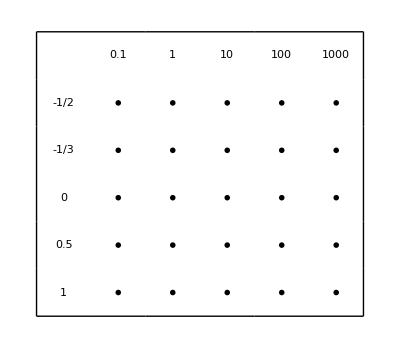

```mathematica
κValues={-1/2, -1/3,0,0.5,1};
σValues={0.1,1,10,100,1000};
Domain=1000;GraphicsGrid[
Prepend[{""}~Join~σValues][MapThread[Prepend,{
DistTable,
Map[Text][κValues]
}]],
Frame->True,
PlotLabel->"Coupled Gaussians, Coupling vs Scale"
]
```

The coupled mean of the coupled distributions will follow the coupled log average (Definition 2 of Nelson, et. al. 2017).  This will require development of an integral form of the coupled mean.

### Question about Definition of Coupled Mean

A careful check of the definition of the Coupled Average Uncertainty is needed to make sure that its consistent with hte definition of the Coupled n^th Moment. The Coupled n^th Moment is defined as
	⟨x_i^n⟩_κ≡∑_(i=1)^N x_i^n P_i^(n, κ)=(∑_(i=1)^N x_i^n p_i^(1+n κ/(1+κ)))/(∑_(i=1)^N p_i^(1+n κ/(1+κ))).
What’s interesting about this expression is that α has dropped out, so the relationship is not based on r=-ακ/(1+κ). The derivation of the weighted generalized mean comes from the generalized log average.  The power of the generalized log  ln_κ x_κ^-α=1/κ(x^(-ακ/(1+κ))-1) is r=-ακ/(1+κ). So following the definition of the coupled moment gives 
	⟨x_i^r⟩_κ≡∑_(i=1)^N x_i^r P_i^(r, κ)=(∑_(i=1)^N x_i^r p_i^(1+r κ/(1+κ)))/(∑_(i=1)^N p_i^(1+r κ/(1+κ))).
The probability is then raised to the power 1+r κ/(1+κ)=1+-(α(κ/(1+κ)))^2rather than 1 + r.  
	There is an inconsistency in the expressions which may need to be explored. I will say that the main result of the paper “On the average uncertainty of systems with nonlinear coupling” shows that using the power 1 + r for the coupled probability leads to a definition for the average uncertainty which is consistent with the generalized information theory.  In particular this form gives the minimum probability for the corresponding coupled-Gaussian and the result that the coupled average is equal to the density at the mean + the coupled standard deviation. On the other hand the coupled mean has the strong results of the coupled-mean and coupled-mean-square leading to the generalization of the standard deviation.  Its seems odd that these two definitions are not completely aligned.
	A possible reconciliation is to treat the coupled average as the coupled mean to the α power
	⟨x_i^α⟩_κ≡∑_(i=1)^N x_i^α P_i^(α, κ)=(∑_(i=1)^N x_i^α p_i^(1+α κ/(1+κ)))/(∑_(i=1)^N p_i^(1+α κ/(1+κ))).
Even so, there is an interesting distinction between the power of x and the power of the coupled probability. If x is now a probability.  The relationship can also be inverted if the generalized log-average is viewed as the starting point with power r, than what κ gives the equivalent expression? The coupled average uncertainty expression is equivalent to κ->∞
	⟨x_i^r⟩_∞≡∑_(i=1)^N x_i^r P_i^(r, ∞)=(∑_(i=1)^N x_i^r p_i^(1+r))/(∑_(i=1)^N p_i^(1+r)), 
with x_i=q_i, another probability.  Strange!
	The mystery is resolved by considering the power of the underlying probability.  Since q~x^(-(1+1/κ)) the power of q^r=x^α thereby explain the use of P_i^(α, κ) as the coupled probability.

### Coupled Mean of Two State Examples

## Coupled ELBO Assessment Example

### Description of Coupled ELBO Assessment

The Evidence Lower Bound (ELBO) is composed of two components the divergence between the latent posterior and prior probabilities and log-likelihood of the data reconstruction. In  log-space the coupled components are additive, thus in the probability space the components are combined using the coupled product.

### Coupled Log-Likelihood

The ELBO training cost function measures the log-likelihood of the reconstructed images, treating each pixel and image as independent. For the assessment, a cross-entropy between the original data and the reconstructed data is measured.

Question: p(x_i|z_i) represents the probability of the data x (an image for instance) given a latent variable z. Put the algorithm seems to be measuring the p(white) and p(black) for each image.  How does this represent the probability of the reconstruction be a sample from the data?

#### Source and Generated Images